## Movimiento armónico entre partículas conectadas por resortes

### Jorge Garza, Febrero de 2016

Si la solución para el desplazamiento es

```mathematica
z[ω_,t_]:=a1*Cos[ω t]+b1*Sin[ω t];
```

Entonces los coeficientes se fijan al imponer las condiciones iniciales z (0) = α y z' (0) = β.

```mathematica
Solve[{z[ω,0]==α,(D[z[ω,t],t]/.t->0)==β},{a1,b1}]
```

Por lo tanto, se tienen las expresiones para el desplazamiento y la posición de cada partícula

### Dos partículas conectadas por tres resortes

```mathematica
Δx[α_,β_,ω_,t_]:=α*Cos[ω t]+(β/ω)*Sin[ω t];
x1[α_,β_,ω_,t_]:=x1e+modo[[1]]*Δx[α,β,ω,t];
x2[α_,β_,ω_,t_]:=x2e+modo[[2]]*Δx[α,β,ω,t];
```

```mathematica
matriz={{(k1+k2)/m1,-k2/m1},{-k2/m2,(k2+k3)/m2}};
```

```mathematica
MatrixForm[matriz]
```

```mathematica
valores=Eigenvalues[matriz];
vectores=Eigenvectors[matriz];
```

```mathematica
Clear[k,m];
interes=2;
(* A continuación se obtiene el resultado deseado en términos de m y k. Intente varios valores de m2, por ejemplo m2=100*m o m2=m *)
raiz=valores[[interes]]/.k3->k/.k2->k/.k1->k/.m2->m/.m1->m
modo=vectores[[interes]]/.k3->k/.k2->k/.k1->k/.m2->m/.m1->m
(* Posiciones de equilibrio *)
x1e=2;
x2e=4;
(* Condiciones iniciales *)
α1=+0.1;
α2=+0.1;
β1=0.;
β2=0.;
(* Valores de m y k*)
m=1;
k=1/100;
ω=Sqrt[raiz];
Print["Posiciones iniciales: x1=",x1[α1,β1,ω,0],", x2=",x2[α2,β2,ω,0]]
Plot[{x1[α1,β1,ω,t],x2[α2,β2,ω,t]},{t,0,100}]
Manipulate[
Show[Graphics[{PointSize[Large],Point[{x1[α1,β1,ω,0.1*t],0}],Point[{x2[α2,β2,ω,0.1*t],0}],Line[{{x1[α1,β1,ω,0.1*t],0},{x2[α2,β2,ω,0.1*t],0}}]}],PlotRange->{{x1e-1,x2e+1},Automatic}],{t,0,2500}]
```

### Tres partículas conectadas por dos resortes

```mathematica
Δx[α_,β_,ω_,t_]:=α*Cos[ω t]+(β/ω)*Sin[ω t];
x1[α_,β_,ω_,t_]:=x1e+modo[[1]]*Δx[α,β,ω,t];
x2[α_,β_,ω_,t_]:=x2e+modo[[2]]*Δx[α,β,ω,t];
x3[α_,β_,ω_,t_]:=x3e+modo[[3]]*Δx[α,β,ω,t];
```

```mathematica
matriz={{k1/m1,-k1/m1,0},{-k1/m2,(k1+k2)/m2,-k2/m2},{0,-k2/m3,k2/m3}};
```

```mathematica
MatrixForm[matriz]
```

```mathematica
valores=Eigenvalues[matriz];
vectores=Eigenvectors[matriz];
```

```mathematica
Clear[k,m];
interes=3;
(* A continuación se obtiene el resultado deseado en términos de m y k. Intente varios valores de m1,m2 y m3, por ejemplo m3=100*m o m3=m *)
raiz=valores[[interes]]/.k2->k/.k1->k/.m3->m/.m2->m/.m1->m
modo=vectores[[interes]]/.k2->k/.k1->k/.m3->m/.m2->m/.m1->m
(* Posiciones de equilibrio *)
x1e=1;
x2e=3;
x3e=5;
(* Condiciones iniciales *)
α1=1/10;
α2=1/10;
α3=1/10;
β1=0.;
β2=0.;
β3=0.;
(* Valores de m y k*)
m=1;
k=1/100;
ω=Sqrt[raiz];
Print["Posiciones iniciales: x1=",x1[α1,β1,ω,0],", x2=",x2[α2,β2,ω,0],", x3=",x3[α3,β3,ω,0]]
Plot[{x1[α1,β1,ω,t],x2[α2,β2,ω,t],x3[α3,β3,ω,t]},{t,0,100}]
Manipulate[
Show[Graphics[{PointSize[Large],Point[{x1[α1,β1,ω,0.1*t],0}],Point[{x2[α2,β2,ω,0.1*t],0}],Point[{x3[α3,β3,ω,0.1*t],0}],Line[{{x1[α1,β1,ω,0.1*t],0},{x2[α2,β2,ω,0.1*t],0}}],Line[{{x2[α2,β2,ω,0.1*t],0},{x3[α3,β3,ω,0.1*t],0}}]}],PlotRange->{{-1+x1e,x3e+1},Automatic}],{t,0,2500}]
```

### Partícula idéntica en una celda cristalina en una dimensión

Las siguientes dos líneas son para obtener la solución particular (se imponen condiciones a la frontera)

```mathematica
z[ω_,t_,n_]:=a1*Cos[ω t-q n a]+b1*Sin[ω t-q n a];
Solve[{z[ω,0,n]==α,(D[z[ω,t,n],t]/.t->0)==β},{a1,b1}]
```

```mathematica
ω[q_,k_,m_]:=2Sqrt[k/m]Sqrt[Sin[a q /2]^2];
a1[α_,β_,q_,a_,n_]:=α Cos[a n q]+(β/ω[q])Sin[a n q];
b1[α_,β_,q_,a_,n_]:=(β/ω[q])Cos[a n q]-α Sin[a n q];
Δxn[α_,β_,q_,a_,n_,k_,m_,t_]:=a1[α,β,q,a,n]*Cos[ω[q,k,m] t-q n a]+b1[α,β,q,a,n]*Sin[ω[q,k,m] t-q n a];
xn[α_,β_,q_,a_,n_,k_,m_,xi_,t_]:=xi+Δxn[α,β,q,a,n,k,m,t]
```

```mathematica
(* Posiciones de equilibrio *)
a=2;
celdas=13;(* El número de partículas debe ser impar *)
xi=Table[i*a,{i,-(celdas-1)/2,(celdas-1)/2}];
(* Condiciones iniciales *)
alfa=Table[2a/10,{i,1,celdas}];
beta=Table[0.0,{i,1,celdas}];
identifica=Table[i,{i,-(celdas-1)/2,(celdas-1)/2}];
(* Valores de m y k*)
m=1;
k=1/10;
Clear[q];
Plot[ω[q,k,m],{q,-Pi/a,Pi/a},PlotLabel->"Relación de Dispersión"]
velocidad=D[ω[q,k,m],q];
Plot[velocidad/.q->vector,{vector,-Pi/a,Pi/a},PlotLabel->"Velocidad de Grupo"]
q=Pi/(400a);
posiciones=Table[xn[alfa[[n]],beta[[n]],q,a,identifica[[n]],k,m,xi[[n]],t],{n,1,celdas}];
(*Plot[posiciones,{t,0,100}];*)
Print["Animación de la oscilación"]
onda=Plot[Cos[q(1) x],{x,-(celdas-1)*a/2-2a,(celdas-1)*a/2+2a},PlotRange->{{-(celdas-1)*a/2-2a,(celdas-1)*a/2+2a},{-1,1}}];
Manipulate[puntos=Table[{posiciones[[i]],0},{i,1,celdas}];
Show[onda,Graphics[{PointSize[Large],Point[puntos]/.t->0.1*tiempo},PlotRange->{{-(celdas-1)*a/2-2a,(celdas-1)*a/2+2a},{-1,1}}]],{tiempo,0,2500}]
```

### Dos partículas diferentes en una celda cristalina unidimensional

```mathematica
μ[m1_,m2_]:=(m1*m2)/(m1+m2);
mT[m1_,m2_]:=m1+m2;
ω[q_,k1_,k2_,m1_,m2_]:=Sqrt[(k1+k2)/(2*μ[m1,m2])-Sqrt[(k1+k2)^2+8k1*k2*μ[m1,m2](Cos[q a]-1)/mT[m1,m2]]/(2*μ[m1,m2])]
a1[α_,β_,q_,a_,n_,k1_,k2_,m1_,m2_]:=-α Cos[a n q]-(β/ω[q,k1,k2,m1,m2])Sin[a n q];
b1[α_,β_,q_,a_,n_,k1_,k2_,m1_,m2_]:=(β/ω[q,k1,k2,m1,m2])Cos[a n q]-α Sin[a n q];
Δxn[α_,β_,q_,a_,n_,k1_,k2_,m1_,m2_,t_]:=a1[α,β,q,a,n,k1,k2,m1,m2]*Cos[ω[q,k1,k2,m1,m2] t-q n a]+b1[α,β,q,a,n,k1,k2,m1,m2]*Sin[ω[q,k1,k2,m1,m2] t-q n a];
xn[α_,β_,q_,a_,n_,k1_,k2_,m1_,m2_,xi_,t_]:=xi+Δxn[α,β,q,a,n,k1,k2,m1,m2,t];
```

```mathematica
(* Posiciones de equilibrio *)
a=2; (* Parámetro de celda *)
celdas=11;(* El número de celdas debe ser impar *)
xi1=Table[(i+0.3)*a,{i,-(celdas-1)/2,(celdas-1)/2}];
xi2=Table[(i+0.6)*a,{i,-(celdas-1)/2,(celdas-1)/2}];
(* Condiciones iniciales *)
alfa=Table[5a/100,{i,1,celdas}];
beta=Table[0.0,{i,1,celdas}];
identifica=Table[i,{i,-(celdas-1)/2,(celdas-1)/2}];
(* Valores de k1,k2, m1 y m2*)
k1=1;
k2=2k1;
m1=1;
m2=m1;
Clear[q]
Plot[ω[q,k1,k2,m1,m2],{q,-Pi/a,Pi/a},PlotLabel->"Relación de Dispersión"]
velocidad=D[ω[q,k1,k2,m1,m2],q];
Plot[velocidad/.q->vector,{vector,-Pi/a,Pi/a},PlotLabel->"Velocidad de Grupo"]
q=Pi/(2a);
Print["Frecuencia=",ω[q,k1,k2,m1,m2]];
posiciones1=Table[xn[alfa[[n]],beta[[n]],q,a,identifica[[n]],k1,k2,m1,m2,xi1[[n]],t],{n,1,celdas}];
posiciones2=Table[xn[alfa[[n]],beta[[n]],q,a,identifica[[n]],k1,k2,m1,m2,xi2[[n]],t],{n,1,celdas}];
(*Plot[{posiciones1,posiciones2},{t,0,100}]*)
puntos1=Table[{posiciones1[[i]],0},{i,1,celdas}]//N;
puntos2=Table[{posiciones2[[i]],0},{i,1,celdas}]//N;
onda=Plot[Cos[q(1) x],{x,-(celdas-1)*a/2-2a,(celdas-1)*a/2+2a},PlotRange->{{-(celdas-1)*a/2-2a,(celdas-1)*a/2+2a},{-1,1}}];
Manipulate[g1=Graphics[{PointSize[Large],Red,Point[puntos1]/.t->0.1*hola},PlotRange->{{-(celdas-1)*a/2-1,(celdas-1)*a/2+a},{-1,1}}];
g2=Graphics[{PointSize[Medium],Blue,Point[puntos2]/.t->0.1*hola},PlotRange->{{-(celdas-1)*a/2-a,(celdas-1)*a/2+a},{-1,1}}];
Show[g1,g2,onda],{hola,0,1000}]
```

### Oscilaciones en una malla bidimensional

```mathematica
parte1[l_]:=1-Cos[l];
ω[lx_,ly_,kx_,ky_,m]:=Sqrt[2*(kx/m)*parte1[lx]+2*(ky/m)*parte1[ly]];
```

```mathematica
kx=1;
ky=kx;
m=1;
g1=Plot3D[ω[lx,ly,kx,ky,m],{lx,-4Pi,4Pi},{ly,-4Pi,4Pi},Mesh->None]
```

-Graphics3D-

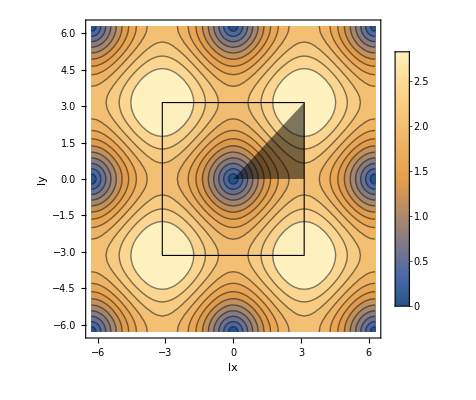

```mathematica
cuadrado=Polygon[{{-Pi,-Pi},{Pi,-Pi},{Pi,Pi},{-Pi,Pi}}];
g1=Graphics[{Opacity[0.5],Polygon[{{0,0},{Pi,0},{Pi,Pi}}]}];
g3=ContourPlot[ω[lx,ly,kx,ky,m],{lx,-2Pi,2Pi},{ly,-2Pi,2Pi},Contours->12,PlotLegends->Automatic,FrameLabel->{"lx","ly"}];
g4=Show[g3,g1,Graphics[{EdgeForm[Dashed],Opacity[0.01],cuadrado}]]
```

```mathematica
g1=ListPlot[Table[{i*0.01*Pi,ω[i*0.01*Pi,0,kx,ky,m]},{i,1,100}],Joined->True,PlotRange->{{0,3Pi},{0,Pi}}]:
```

```mathematica
g2=ListPlot[Table[{Pi+i*0.01*Pi,ω[Pi,i*0.01*Pi,kx,ky,m]},{i,1,100}],Joined->True,PlotRange->{{0,3Pi},{0,Pi}}];
```

```mathematica
g3=ListPlot[Table[{2Pi+i*0.01*Pi,ω[Pi-i*0.01*Pi,Pi-i*0.01*Pi,kx,ky,m]},{i,1,100}],Joined->True,PlotRange->{{0,3Pi},{0,Pi}}];
```

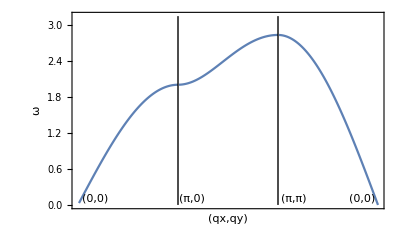

```mathematica
g4=Show[g1,g2,g3,Graphics[{Line[{{Pi,0},{Pi,Pi}}],Text["(0,0)",{0.55,.1}],Text["(π,0)",{Pi+.45,.1}],Text["(π,π)",{2Pi+0.5,.1}],Text["(0,0)",{3Pi-0.5,.1}]}],Graphics[Line[{{2Pi,0},{2Pi,Pi}}]],FrameTicks->{None,Automatic},Frame->True,FrameLabel->{"(qx,qy)","ω"}]
```

```mathematica
Export["Figura_omega_2D_4.png",g4]
```

Figura_omega_2D_4.png